```mathematica
Do[If[x^2+y^2+z^2==t^2&&con,Print[{x,y,z,t}]],{x,30},{y,x-1},{z,y-1},{t,100}]
```

{12,9,8,17}

{15,10,6,19}

{16,15,12,25}

{20,12,9,25}

{21,16,12,29}

{21,18,14,31}

{22,21,6,31}

{24,18,16,34}

{25,20,8,33}

{26,18,15,35}

{26,22,19,39}

{27,14,6,31}

{28,21,12,37}

{29,22,14,39}

{29,28,20,45}

{30,20,12,38}

{30,25,18,43}

```mathematica
NestList[Sin,5,5]//N
```

```mathematica
{5.,-0.9589242746631385,-0.8185741444617193,-0.7301723379367498,-0.6669980469189455,-0.618630196631228}
```

```mathematica
f[d_,x_,y_]:=BlockMap[{{#1,#2},{#2,#2}}&@@##&,NestList[d,x,y]//N,2,1]//Flatten[#,1]&
```

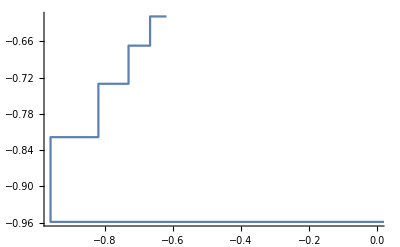

```mathematica
{{5.,-0.9589242746631385},{-0.9589242746631385,-0.9589242746631385},{-0.9589242746631385,-0.8185741444617193},{-0.8185741444617193,-0.8185741444617193},{-0.8185741444617193,-0.7301723379367498},{-0.7301723379367498,-0.7301723379367498},{-0.7301723379367498,-0.6669980469189455},{-0.6669980469189455,-0.6669980469189455},{-0.6669980469189455,-0.618630196631228},{-0.618630196631228,-0.618630196631228}}//ListLinePlot
```

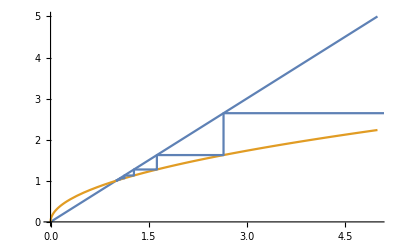

```mathematica
Show@{Plot[{x,x^(1/2)},{x,1-1,5}],f[Sqrt,7,10]//ListLinePlot}
```

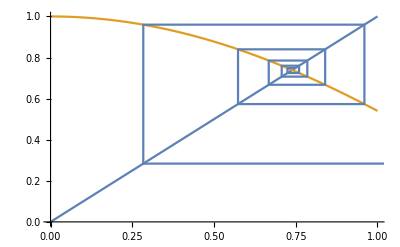

```mathematica
Show@{Plot[{x,Cos[x]},{x,0,1}],f[Cos,5,10]//ListLinePlot}
```